# Modelagem Idempotente para Cabos SC Ajuste das funções via VF

O objetivo desse notebook é apresentar o cálculo dos idempotentes e tentar realizar o ajuste via VF ou OVF

## Início

```mathematica
Clear["Global`*"]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Documents and Settings\Administrador\Escritorio\TESIS DE MESTRADO\CODIGOS MATHEMATICA\Cabos por Matriz IdemPotente (REEVALUAR)\Resultados Linea

```mathematica
<<LCParam`
```

```mathematica
SetOptions[{ListPlot,ListLogPlot,ListLogLogPlot},BaseStyle->{FontFamily->"Helvetica", 14},ImageSize-> 600,Joined-> True,PlotStyle-> Thick,
Axes-> False,Frame-> True];
```

## Opções de programa

```mathematica
SetOptions[{ListPlot,ListLogLinearPlot,ListLogLogPlot},Axes->False,Frame->True,Joined->True,ImageSize->450,PlotStyle->{PointSize[0.015]},BaseStyle->{14,FontFamily->"Helvetica"}];
```

```mathematica
plstyle1={AbsoluteThickness[2],RGBColor[1,0,0]};
plstyle2={AbsoluteThickness[2],RGBColor[0,0,1]};
plstyle3={AbsoluteThickness[2],PointSize[.015],RGBColor[0,1,0]};
```

## Configuração da Rede

```mathematica
xc={0};
 yc={11};
mostra=Table[{Circle[{xc[[i]],yc[[i]]},0.25]},{i,1,Length[xc]}];
tsimples=Show[Graphics[mostra],AspectRatio->Automatic,Axes->False,Frame->Automatic,PlotRange->{{-15,15},{0,45}},FrameLabel->{"distância (m)","distância (m)"}]
```

-Graphics-

## Dados de Entrada

```mathematica
ncond=Length[xc];
nfeixe=1;
nfases=1;
npr=0;
```

```mathematica
(* rf=.908 *10^-2; *)
rf=22*10^-3/2;
rint=0.1*10^-3/2; 
rpr=0;
```

```mathematica
ϵ=8.854 10^-12;
```

```mathematica
ρc=0.1052*10^-3 * π* rf^2;
ρpr=4.19*10^-3* π  *rpr^2;
```

```mathematica
ρsolo= 100;
(*tempfase=60;
fencalum=0.750223;
αtemp=0.00454562;
σc=fencalum/(ρ00(1+αtemp tempfase));
ρc=1/σc;*)
```

```mathematica
compr=25000;
```

```mathematica
sigma=1/ρsolo;
(*kprima[sigma_,Omega_]:=(sigma)+(10^-6)*(0.057849+I*0.12097)*(Omega^0.71603);*)
kprima[sigma_,Omega_]:=(sigma);
G1=DiagonalMatrix[Table[10^-12,{nfases}]];
```

## Frequências e Inicialização das Listas

### Freqüências de interesse

#### Faixa de Frequência

```mathematica
d1=-1;
d2=N[7.,40];
n=15;
freqlog[i_,f_,np_]:=Table[N[10^(i+x(f-i)/(Floor[np]-1))],{x,0,np-1}]
freqlin[i_,f_,np_]:=Table[N[(i+x(f-i)/(Floor[np]-1))],{x,0,np-1}]
(*f0=freqlog[d0,d1,500];*)
f1=freqlog[d1,d2,n];
f2=freqlin[10^d1, 10^d2,n];
f=Sort@Join[f2,f1];
nf=Length[f];
```

```mathematica
sk=2*π*f;
nf=Length[sk]
```

30

### Inicialização das listas

```mathematica
T=T1=λ0=Γ1=Yc1=Af1=Am1=Am2=M1=γm=Table[0,{n,1,nf}];
```

## Rotinas Auxiliares

### ROT

```mathematica
rot[s_?MatrixQ]:=Module[{S=s,Nc,SA,SB,scale,ang,scale1,col,scale2,err1,err2,numerator,denominator,aaa,bbb,ccc},
Nc=Length[S];
SA=Table[0,{Nc},{Nc}];
SB=SA;
scale1=Table[0,{Nc}];
scale2=scale=ang=scale1;
err1=scale1;
err2=scale1;

numerator=Table[0,{Nc}];
denominator=numerator=scale1=scale2;

For[col=1,col≤ Nc,col++,
numerator[[col]]=0.;
denominator[[col]]=numerator[[col]]=0.;

For[j=1,j≤ Nc,j++,
numerator[[col]]=numerator[[col]]+Im[S[[j,col]]]*Re[S[[j,col]]];
denominator[[col]]=denominator[[col]]+Re[S[[j,col]]]^2-Im[S[[j,col]]]^2];

numerator[[col]]=-2*numerator[[col]];
ang[[col]]=0.5*ArcTan[denominator[[col]],numerator[[col]]];
scale1[[col]]=Cos[ang[[col]]]+ⅈ*Sin[ang[[col]]];
scale2[[col]]=Cos[ang[[col]]+π/2.]+ⅈ*Sin[ang[[col]]+π/2.];

For[j=1,j≤ Nc,j++,
SA[[j,col]]=S[[j,col]]*scale1[[col]];
SB[[j,col]]=S[[j,col]]*scale2[[col]];];

aaa=0.;
bbb=0.;
ccc=0.;

For[j=1,j≤ Nc,j++,
aaa=aaa+Im[SA[[j,col]]]^2;
bbb=bbb+Re[SA[[j,col]]]*Im[SA[[j,col]]];
ccc=ccc+Re[SA[[j,col]]]^2];

err1[[col]]=aaa*Cos[ang[[col]]]^2+bbb*Sin[N[2*ang[[col]],16]]+ccc*Sin[ang[[col]]]^2;

aaa=0.;
bbb=0.;
ccc=0.;

For[j=1,j≤ Nc,j++,
aaa=aaa+Im[SB[[j,col]]]^2;
bbb=bbb+Re[SB[[j,col]]]*Im[SB[[j,col]]];
ccc=ccc+Re[SB[[j,col]]]^2];

err2[[col]]=aaa*Cos[ang[[col]]]^2+bbb*Sin[N[2*ang[[col]],16]]+ccc*Sin[ang[[col]]]^2;

If[err1[[col]]<err2[[col]],scale[[col]]=scale1[[col]],scale[[col]]=scale2[[col]]];

S[[All,col]]=S[[All,col]]*scale[[col]];
];
Return[S]
]
```

### Elimina o Cruzamento de Autovetores (Newton-Raphson)

```mathematica
eigNR[G_?MatrixQ,V0_,d0_,Tol_:10^-10]:=Module[{A=G,nc,scale,v,d,vec,res,jac,i},
nc=Length[A];
scale=Norm[A];
A=A/scale;
outd=Table[0,{nc}];
outv=Table[0,{nc},{nc}];
itr=0;
jac=Table[0.0,{nc+1},{nc+1}];
Do[{v=V0[[1;;,i]];
d=d0[[i]];
res=Max[Abs[A.v-v*d]];
While[(res>Tol)&& (itr<10000),
itr=itr+1;
jac[[1;;nc,1;;nc]]=A-d*IdentityMatrix[nc];
jac[[1;;nc,nc+1]]=-v;
jac[[nc+1,1;;nc]]=2*v;
res=Join[A.v-v*d,{v.v-1}];
vec=LinearSolve[jac,res];
res=Max[Abs[vec]];
v=v-vec[[1;;nc]];
d=d-vec[[nc+1]];
];
outd[[i]]=d*scale;
outv[[1;;,i]]=Normalize[v];},{i,1,nc}]];
```

### Decompor Matriz (n x n) em elementos

```mathematica
descompmatrlargaAsimetrica[Matr_]:=Module[{kk,nm,Matr2},
Matr2=Table[0,{N[Max[Dimensions[Matr]]]},{N[Min[Dimensions[Matr]]]*(N[Min[Dimensions[Matr]]])}];
For[nm=1,nm≤N[Max[Dimensions[Matr]]],nm++,
kk=0;
Table[kk++;Matr2[[nm,kk]]=Matr[[nm,i,j]],{i,1,N[Min[Dimensions[Matr]]]},{j,1,N[Min[Dimensions[Matr]]]}]];
Return[Matr2]]
```

### UnwrapPhase

```mathematica
(***********UnwrapPhase follows*************)UnwrapPhase[data_?VectorQ,tol_:Pi,inc_:2 Pi]:=FixedPoint[#+inc*FoldList[Plus,0.,Sign[Chop[ListCorrelate[{1,-1},#],tol]   (*close Chop*)]    (*close Sign*)]&,(*close FoldList*)data]   (*close FixedPoint and overall function*)

UnwrapPhase[list:{{_,_}..}]:=Transpose[{list[[All,1]],UnwrapPhase[list[[All,-1]]]}]
(***********UnwrapPhase above*************)
```

## Principal Loop de Frequência

```mathematica
YNodal=ytraco=gamma=Evals=T2=Table[0,{nf}];
```

```mathematica
AbsoluteTiming[Do[{ω=sk[[nm]],
MontaMatrizes[ncond,npr,nfeixe,kprima[sigma,ω],ρc,ρpr,rf,rint,rpr,xc,yc,ω],
(*MontaMatrizessemp[ncond,npr,nfeixe,sigma,ρc,ρpr,rf,rint,rpr,xc,yc,ω]*)
Yn=Ynodal[Z1,Y1,compr];
ytraco[[nm]]=Tr[Yn],

Γ= N[Y1.Z1,40],
gamma[[nm]]=Γ;
nc=Length[Z1];
k=nm,

If[k==1,
{eval,evec}=Eigensystem[Γ];
 evelho=rot[Transpose[evec]],
eigNR[Γ,evelho,eval];
eval=outd;
evelho=outv;
],
λ0[[nm]]=Sqrt[eval];
α1=Exp[-λ0[[nm]] compr];
Am1[[nm]]=α1;
Am2[[nm]]=α1 Exp[I ω tau],
T[[nm]]=evelho,
Evals[[nm]]=eval,

Afase=evelho.DiagonalMatrix[Am1[[nm]]].Inverse[evelho]; (*corregido*)
Af1[[nm]]=Select[Flatten[UpperTriangularize[Afase]],Abs[#1]>0&];
(* creating idempotents matrices  for inclusion of time delay multiply by αi, e.g. 
M5[[nm]]=Transpose@{evect[[All,5]]}.{evect[[5,All]]} α1[[5]]*)
(*M1[[nm]]=Table[Transpose@{evelho[[All,i]]}.{Inverse[evelho][[i,All]]} α1[[i]],{i,3}];   (*corregido*)*)

},{nm,1,nf}]]
```

{0.078125,Null}

```mathematica
nc=Length[Afase]
```

1

```mathematica
ListLogLinearPlot[Transpose@{f,UnwrapPhase[Arg[Am2[[All,1]]]]},Joined->True,PlotRange->All]
```

-Graphics-

```mathematica
du=1/π Integrate[
```

```mathematica
Hang=(π/2.)(Log[Am1[[Floor[nf/2+1]]]]-Log[Am1[[Floor[nf/2]]]])/(Log[sk[nf/2+1]]-Log[sk[Floor[nf/2]]]);
```

```mathematica
τ=compr Im[λ0[[nf]]]/ω+Arg[α1]/ω
```

{0.0000838}

```mathematica
compr/(3*10^8)//N
```

0.0000833333

Backwinding dos idempotentes pela multiplicação do H obtido com os tempos de trânsito dos diversos modos

```mathematica
sk[[1]]
```

0.628319

```mathematica
Am1Tr=Tr[Am1[[#]]]&/@Range[1,nf]
```

{0.999614-0.000392302 ⅈ,0.999614-0.000392302 ⅈ,0.999271-0.000775371 ⅈ,0.998692-0.00162539 ⅈ,0.997973-0.00405373 ⅈ,0.997282-0.0130289 ⅈ,0.995015-0.0463661 ⅈ,0.977399-0.165907 ⅈ,0.800625-0.554433 ⅈ,-0.52675-0.751197 ⅈ,-0.0215612-0.758596 ⅈ,-0.417781+0.13635 ⅈ,-0.0859775+0.0706523 ⅈ,-0.00425624+0.00342362 ⅈ,0.00492723-0.0020329 ⅈ,-0.000248476+0.000258932 ⅈ,-0.0000417845+0.0000109445 ⅈ,2.23669×10^-6+0.0000106456 ⅈ,-5.74659×10^-6-4.29691×10^-6 ⅈ,2.78816×10^-7-1.44173×10^-6 ⅈ,3.47044×10^-7-3.59149×10^-8 ⅈ,2.55512×10^-8+8.92948×10^-8 ⅈ,-2.53222×10^-8+9.54775×10^-9 ⅈ,-3.03858×10^-9-7.92881×10^-9 ⅈ,2.70197×10^-9-8.57854×10^-10 ⅈ,1.92784×10^-10+9.79263×10^-10 ⅈ,-3.67723×10^-10+1.25657×10^-11 ⅈ,2.35363×10^-11-1.39264×10^-10 ⅈ,5.16375×10^-11+2.21766×10^-11 ⅈ,5.16375×10^-11+2.21766×10^-11 ⅈ}

```mathematica
Dimensions[Am1]
Dimensions[Am1Tr]
```

{30,1}

{30}

# Implementação do ORVF

## Dados de Entrada

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
FileNames["*.txt"];
```

```mathematica
tmin=compr/(3*10^8);
tmax=1.02*tmin;
num=150;
```

```mathematica
tau=Table[(tmin+i (tmax-tmin)/num),{i,1,num}];
```

```mathematica
omega=sk;
```

### Polos Iniciais

```mathematica
fmax=Last@omega;
fmin=First@omega;
npolini=15;
```

```mathematica
polini=Flatten[Table[{-(ff)/100+ⅈ*(ff),-(ff)/100-ⅈ*(ff)},{ff,fmin,fmax,(fmax-fmin)/((npolini-1)/2)}]];
```

```mathematica
erroRMS=Table[0,{num},{Min[Dimensions[Am1]]}];
```

# Vector Fitting

### Funções Auxiliares

```mathematica
idx[polos_List]:=Module[{np,fun,ind},
np=Length[polos];
ind=0*Range[1,np];
fun=Map[Head,polos];
Do[If[fun[[mm]]==Complex,
If[mm==1,ind[[mm]]=1,
If[ind[[mm-1]]==0 ∨ ind[[mm-1]]==2 ,ind[[mm]]=1;ind[[mm+1]]=2,
ind[[mm]]=2]]],{mm,1,np}];
Return[ind]];

Aux[s_,p_List,index_List]:=With[
{np=Length[p]},
Table[If[index[[mm]]==0.,
(1/(s-p[[mm]])),If[index[[mm]]==1.,
(1/(s-p[[mm]])+1/(s-p[[mm+1]])),
(ⅈ/(s-p[[mm-1]])-ⅈ/(s-p[[mm]]))]],
{mm,np}]];

Aux2[s_,p_List,index_List]:=With[
{np=Length[p]},
Table[If[index[[mm]]==0.,
(Sqrt[2*Abs[p[[mm]]]])/(s-p[[mm]])*Product[(s+Conjugate[p[[kk]]])/(s-p[[kk]]),
{kk,1,mm-1}],
If[index[[mm]]==1.,
(Sqrt[-2*Re[p[[mm]]]])*(s-Abs[p[[mm]]])/((s-p[[mm]])*(s-p[[mm+1]]))*Product[(s+Conjugate[p[[kk]]])/(s-p[[kk]]),
{kk,1,mm-1}],
(Sqrt[-2*Re[p[[mm]]]])*(s+Abs[p[[mm]]])/((s-p[[mm-1]])*(s-p[[mm]]))*Product[(s+Conjugate[p[[kk]]])/(s-p[[kk]]),
{kk,1,mm-2}]]],
{mm,np}]];
```

# Cálculos dos Pólos com o RVF

```mathematica
RVFpolos[polos_List,freq_List,data_,termoD_:1,termoE_:1]:=Module[{npol,nfreq,ss,indices,Anum,UmS,Anum2,Af,AA,BB,XX,naux,Csigma,Azeros,Bzeros,Czeros,Dzeros,polaux,polosN,weight,Ws,RVF,i,j,q,r,AAA,BBB,AAAT,normas,Xaux,AAAaux,AAAscale,scale},
npol=Length[polos];
nfreq=Length[freq];
ss=ⅈ*N[freq];

indices=idx[polos];
Anum=Transpose[Aux[ss[[Range[nfreq]]],polos,indices]];

UmS=If[termoD==1∧termoE==1,{1,ss[[#]]}&/@Range[nfreq],
If[termoD==1∧termoE==0,{1}&/@Range[nfreq],
If[termoD==0∧termoE==1,{ss[[#]]}&/@Range[nfreq],{}&/@Range[nfreq]]]];
Anum2=-data*Anum;

weight=Table[1,{nfreq}];
Ws=Norm[Table[weight[[i]]*data[[i]],{i,1,nfreq}]]/nfreq;

RVF=Flatten[{Table[0,{npol+termoD+termoE}],Table[Sum[Re[Anum[[i,j]]],{i,1,nfreq}],{j,1,npol}],nfreq}]*Ws;
Af=Flatten[{Anum[[#]],UmS[[#]],Anum2[[#]],-data[[#]]}*weight[[#]]]&/@Range[nfreq];
AA=Join[Re[Af],Im[Af],{RVF}];
BB=Flatten[{0*Range[1,2*nfreq],nfreq}]*Ws;

AAA=Take[QRDecomposition[AA][[2]],-npol-1,-npol-1];
BBB=Take[QRDecomposition[AA][[1]],-npol-1].BB;

AAAT=Transpose[AAA];
normas=Norm[AAAT[[#]]]&/@Range[1,npol+1];
AAAaux=AAAT/normas;

AAAscale=Transpose[AAAaux];
Xaux=LeastSquares[AAAscale,BBB];
scale=1/normas;
XX=Xaux*scale;

naux=termoD+termoE;

Azeros=Table[0,{npol},{npol}];
Bzeros=Table[{0},{npol}];
Bzeros=Table[If[indices[[mm]]==0,Bzeros[[mm]]=1,If[indices[[mm]]==1,Bzeros[[mm]]=2,0]],{mm,npol}];Bzeros=Partition[Bzeros[[Range[1,npol]]],1];
Czeros=Partition[XX[[Range[1,npol]]],1];
Dzeros=XX[[-1]];

Do[If[indices[[mm]]== 0,Azeros[[mm,mm]]=polos[[mm]],If[indices[[mm]]== 1,Azeros[[mm,mm]]=Re[polos[[mm]]];Azeros[[mm,mm+1]]=Im[polos[[mm]]];Azeros[[mm+1,mm]]=-Im[polos[[mm]]];Azeros[[mm+1,mm+1]]=Re[polos[[mm]]]],0],{mm,npol}];

polaux=Eigenvalues[Azeros-(Bzeros/Dzeros).Transpose[Czeros]];
polosN=-Abs[Re[polaux]]+ⅈ Im[polaux];

Return[polosN]]
```

# Cálculo dos Resíduos

### Cálculo dos Resíduos

```mathematica
res[polos_List,freq_List,data_List,termoD_:1.,termoE_:1.]:=Module[{npol,nfreq,ss,indices,AAnum,UUmS,AAf,AAff,AAffT,normas,BBff,XXff,resfim,dd,ee,naux,AAAaux,AAAscale,Xaux,scale},
npol=Length[polos];
nfreq=Length[freq];
ss=ⅈ*N[freq];

indices=idx[polos];

AAnum=Transpose[Aux[ss[[Range[nfreq]]],polos,indices]];

UUmS=If[termoD==1∧termoE==1,{1,ss[[#]]}&/@Range[nfreq],
If[termoD==1∧termoE==0,{1}&/@Range[nfreq],
If[termoD==0∧termoE==1,{ss[[#]]}&/@Range[nfreq],{}&/@Range[nfreq]]]];

AAf=Flatten[{AAnum[[#]],UUmS[[#]]}]&/@Range[nfreq];

AAff=ArrayFlatten[{{Re[AAf]},{Im[AAf]}}];
BBff=Flatten[{Re[data],Im[data]}];

naux=termoD+termoE;

AAffT=Transpose[AAff];
normas=Norm[AAffT[[#]]]&/@Range[1,npol+naux];
AAAaux=AAffT/normas;

AAAscale=Transpose[AAAaux];
Xaux=LeastSquares[AAAscale,BBff];
scale=1/normas;
XXff=Xaux*scale;

resfim=0*Range[1,npol];

Do[If[indices[[nm]]==0,resfim[[nm]]=XXff[[nm]],If[indices[[nm]]==1,resfim[[nm]]=XXff[[nm]]+ⅈ*XXff[[nm+1]];resfim[[nm+1]]=XXff[[nm]]-ⅈ*XXff[[nm+1]],0]],{nm,npol}];

If[termoD==1∧termoE==1,dd=XXff[[-2]];ee=XXff[[-1]],
If[termoD==1∧termoE==0,dd=XXff[[-1]];ee=0,
If[termoD==0∧termoE==1,dd=0;ee=XXff[[-1]],dd=0;ee=0]]];

Return[{resfim,dd,ee}]]
```

# Outros Calculos

```mathematica
calcelem[polos_List,residuos_List,omega_List,yElementos_,TermD_,TermE_,nres_]:=Module[{funcoes,Pontos,difRMS,dif,RMSD},

funcoes=Table[Sum[(residuos[[i,kk]]/(s-polos[[kk]])),{kk,Length[polos]}]+TermD[[i]]+s*TermE[[i]],{i,nres}];
Pontos=Transpose[Table[Map[(funcoes[[i]]/.s->#)&,ⅈ omega],{i,nres}]];
dif=Sqrt[Abs[(Pontos-yElementos)^2]/Length[omega]];
RMSD=Sqrt[Total[Abs[Pontos-yElementos]^2]/Length[omega]];

Return[{funcoes,Pontos,RMSD,dif}]]
```

```mathematica
recompmatr[Matr_]:=Module[{ncond2,k,Mrecomp},
ncond2=Solve[Sqrt[2*Min[Dimensions[Matr]]-x]==x,x][[1,1,2]];
Mrecomp=Table[0,{ncond2},{ncond2}];
For[k=1,k<ncond2+1,k++,Mrecomp[[All,k]]=Flatten[{Take[Matr,{k*(k-1)/2+1,k*(k+1)/2}],Table[0,{ncond2-k}]}]];
Table[Mrecomp[[j,i]]=Mrecomp[[i,j]],{i,1,ncond2},{j,1,ncond2}];
Return[{Mrecomp}]]
```

```mathematica
calctraco[polos_List,residuos_List,freq_,data_,termoD_,termoE_]:=Module[{funcoes,Pontos,difRMS,dif},
funcoes=Table[Sum[(residuos[[kk]]/(s-polos[[kk]])),{kk,Length[polos]}]+termoD+s*termoE];
Pontos=Map[(funcoes/.s->#)&,ⅈ freq];
difRMS=Sqrt[Total[Abs[(Pontos-data)^2]]]/Sqrt[Length[freq]];
dif=Sqrt[Abs[(Pontos-data)^2]]/Sqrt[Length[freq]];
Return[{funcoes,Pontos,difRMS,dif}]]
```

```mathematica
recompmatrlarga[Matr_]:=Module[{YsAux,Ys,k},
YsAux=Table[0,{N[Max[Dimensions[Matr]]]},{N[Min[Dimensions[Matr]]]},{N[Min[Dimensions[Matr]]]}];
For[k=1,k≤ N[Max[Dimensions[Matr]]],k++,YsAux[[k]]=recompmatr[Matr[[k]]]];
Ys=Flatten[YsAux,1];
Return[{Ys}]]
```

```mathematica
descompmatrlarga[Matr_]:=Module[{kk,nm,Matr2},
Matr2=Table[0,{N[Max[Dimensions[Matr]]]},{N[Min[Dimensions[Matr]]]*(N[Min[Dimensions[Matr]]]+1)/2}];
For[nm=1,nm≤N[Max[Dimensions[Matr]]],nm++,
kk=0;
Table[If[ i≥ j,kk++;Matr2[[nm,kk]]=Matr[[nm,i,j]]],{i,1,N[Min[Dimensions[Matr]]]},{j,1,N[Min[Dimensions[Matr]]]}]];
Return[{Matr2}]]
```

```mathematica
recompmatrizesexport[polos_,residuos_,TermD_,TermE_,freq_]:=Module[{SERA,SERB,SERC,SERD,SERE,SERRsinconv,SERpoles,s,n,npol},
n=(Sqrt[1+8*N[Length[residuos]]]-1)/2;
s={freq};
SERA=SparseArray[DiagonalMatrix[Flatten[Table[{polos},{n}]]]//Chop];
npol=Length[polos];
SERB=Table[0,{n*npol},{n}];
Flatten[Table[SERB[[(j-1)*npol+i,j]]=1,{i,1,npol},{j,1,n}]];
{SERD}=recompmatr[TermD];
{SERE}=recompmatr[TermE];
SERRsinconv=Transpose[residuos];
SERC=Table[0,{Length[polos]},{Length[TermD]},{Length[TermD]}];
Table[SERC[[n]]=recompmatr[residuos[[All,n]]][[1]],{n,1,Length[polos]}];
SERC=Transpose[Flatten[SERC,1]];
SERpoles=polos;
Return[{SERA,SERB,SERC,SERD,SERE,SERRsinconv,SERpoles,s}]]
```

# Fitting de ytraco (RVF, polos melhorados para Ynodal)

```mathematica
AbsoluteTiming[Do[
yElementos=Am1[[#]] Exp[I omega[[#]] tau[[mm]]]&/@Range[1,nf];
ytraco=Tr[yElementos[[#]]]&/@Range[nf];

TemD=1.;
TemE=0;
ppolos=N[polini];
niterElem=N[25];

AbsoluteTiming[Do[pp=RVFpolos[ppolos,omega,ytraco,TemD,TemE];ppolos=pp,{niterElem}]];
polosRVF=ppolos;
nres=Min[Dimensions[yElementos]];
residuosRVF=TermDRVF=TermERVF=ConstantArray[0,nres];

Do[{residuosRVF[[nm]],TermDRVF[[nm]],TermERVF[[nm]]}=res[polosRVF,omega,yElementos[[All,nm]],TemD,TemE],{nm,nres}];
{funcoesRVF,PontosRVFElem,difRMSRVF,difRVF}=calcelem[polosRVF,residuosRVF,omega,yElementos,TermDRVF,TermERVF,nres];

erroRMS[[mm]]=difRMSRVF,{mm,num}]]
```

{37.578125,Null}

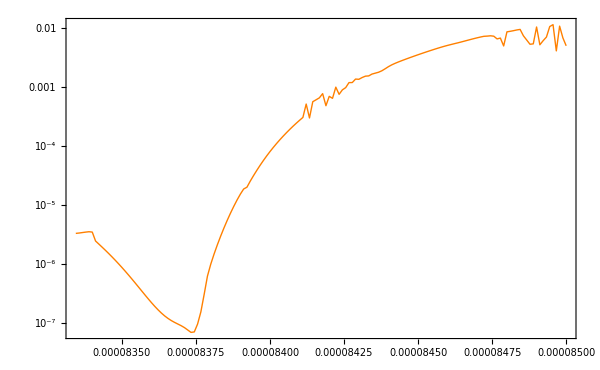

```mathematica
ListLogPlot[Transpose@{tau,erroRMS[[All,#]]}&/@Range[1,nres],Joined->True,PlotRange->All,PlotStyle->{Orange,Thin}]
```

```mathematica
pos=Flatten[Position[erroRMS,Min[erroRMS]]]
```

{36,1}

```mathematica
tau1=tau[[pos[[1]]]];
```

```mathematica
AbsoluteTiming[Do[{ω=sk[[nm]],
Am2[[nm]]=Am1[[nm]] Exp[I ω tau1];
},{nm,1,nf}]]
```

{0.,Null}

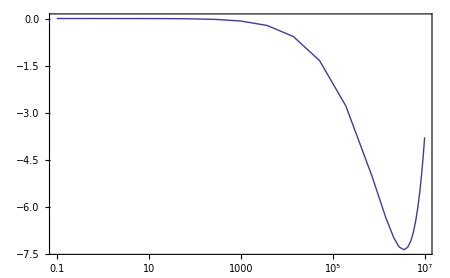

```mathematica
ListLogLinearPlot[Transpose@{f,UnwrapPhase[Arg[Am2[[All,1]]]]},Joined->True,PlotRange->All]
```